# Complex Networks final assignment Communities

## Pablo Rosillo Rodes

Firstly we import the adjacency matrix (not adjacency list).

```mathematica
Adj = Import["AdjacencyMatrixFile.txt","Table","FieldSeparators"->","]
```

{1}
 |  |  |  |

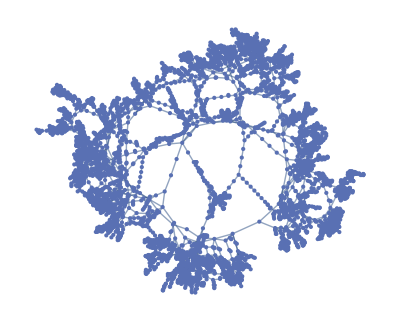

```mathematica
g = AdjacencyGraph[Adj]
```

We compute several community partitions and study their suitability based on their modularity.

```mathematica
comm1 = FindGraphCommunities[g, Method->"Modularity"];
```

```mathematica
mod1 = N[GraphAssortativity[g,comm1,"Normalized"->False]]
```

0.934957

```mathematica
CommunityGraphPlot[g, comm1, Method->"Hierarchical", CommunityLabels->Table[i, {i, 1, 40}]]
```

-Graphics-

```mathematica
comm2 = FindGraphCommunities[g, Method->"Hierarchical"];
```

```mathematica
mod2 = N[GraphAssortativity[g,comm2,"Normalized"->False]]
```

0.854765

```mathematica
CommunityGraphPlot[g, comm2, Method->"Hierarchical"]
```

-Graphics-

```mathematica
comm3 = FindGraphCommunities[g, Method->"Spectral"];
```

```mathematica
mod3 = N[GraphAssortativity[g,comm3,"Normalized"->False]]
```

0.875783

```mathematica
CommunityGraphPlot[g, comm3, Method->"Hierarchical"]
```

-Graphics-

```mathematica
comm4 = FindGraphCommunities[g, Method->"Centrality"];
```

```mathematica
mod4 = N[GraphAssortativity[g,comm4,"Normalized"->False]]
```

0.933016

```mathematica
CommunityGraphPlot[g, comm4, Method->"Hierarchical"]
```

-Graphics-

```mathematica
comm5 = FindGraphCommunities[g, Method->"CliquePercolation"];
```

```mathematica
mod5 = N[GraphAssortativity[g,comm5,"Normalized"->False]]
```

0.153506

```mathematica
CommunityGraphPlot[g, comm5, Method->"Hierarchical"]
```

-Graphics-